# Plots of initial temperature

```mathematica
Clear[plotinitialTemp];
plotinitialTemp[k_,realizations_,currentDir_,nList_,mList_]:=plotinitialTemp[alg,initSolType,k,realizations,seed,currentDir,nList,mList]=Module[
(* Put local variables here *)
{initialTempRawData,initialTempData,index},

Clear[initialTempRawData,initialTempData,index];

initialTempRawData=Import[currentDir<>ToString["data/initialTemp_k=2_100_S=1000_chi0=0.8.csv"]];

(* Initialize plot data *)
initialTempData=ConstantArray[0,{(Length[nList])*Length[mList]}];

(* Process data into an easily plottable form *)
For[i=1,i≤Length[mList],i++,
For[j=1,j≤Length[nList],j++,
index=(i-1)*Length[nList]+j;
initialTempData⟦index⟧={mList⟦i⟧,nList⟦j⟧,initialTempRawData⟦i,j⟧};
];
];

(*Print[StringForm["Plots of experiment for:\nAlgorithm=``\nInitial Solution Type=``\nk-value=``\nEmpirical Data Points=``",alg,initSolType,k,realizations]];*)

(* Plot makespan gap as a percentage between 0 and 20 *)
ListPlot3D[initialTempData,Mesh->All,Filling->Bottom,AxesLabel->{"Machines","Jobs","Makespan Gap\n(percentage)"},ImageSize->400,PlotRange->{0,200}]
];
```

```mathematica
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotinitialTemp[2,100,currentDir,nList,mList]
```

-Graphics3D-

```mathematica
Clear[plotinitialTemp];
plotinitialTemp[k_,realizations_,currentDir_,nList_,mList_]:=plotinitialTemp[alg,initSolType,k,realizations,seed,currentDir,nList,mList]=Module[
(* Put local variables here *)
{initialTempRawData,initialTempData,index},

Clear[initialTempRawData,initialTempData,index];

initialTempRawData=Import[currentDir<>ToString["data/initialTemp_k=2_100_S=1000_chi0=0.8.csv"]];

(* Initialize plot data *)
initialTempData1=ConstantArray[0,Length[mList]];
initialTempData2=ConstantArray[0,Length[mList]];
initialTempData3=ConstantArray[0,Length[mList]];
initialTempData4=ConstantArray[0,Length[mList]];
initialTempData5=ConstantArray[0,Length[mList]];
initialTempData6=ConstantArray[0,Length[mList]];
initialTempData7=ConstantArray[0,Length[mList]];
initialTempData8=ConstantArray[0,Length[mList]];
initialTempData9=ConstantArray[0,Length[mList]];
initialTempData10=ConstantArray[0,Length[mList]];

(* Process data into an easily plottable form *)
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData1⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,1⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData2⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,2⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData3⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,3⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData4⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,4⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData5⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,5⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData6⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,6⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData7⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,7⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData8⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,8⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData9⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,8⟧};
];
For[i=1,i≤Length[mList],i++,
index=i;
initialTempData10⟦index⟧={mList⟦i⟧,initialTempRawData⟦i,8⟧};
];

marker1=Graphics[{plotColour,Disk[]}];
ListPlot[{initialTempData1,initialTempData2,initialTempData3,initialTempData4,initialTempData5,initialTempData6,initialTempData7,initialTempData8,initialTempData9,initialTempData10},AxesLabel->{"Machines","Initial Temperature T"},ImageSize->400,Ticks->Automatic,Joined->True,PlotMarkers->{●,10},PlotStyle->{plotColour},PlotLegends->{"n=10","n=20","n=30","n=40","n=50","n=60","n=70","n=80","n=90","n=100"}]
];
```

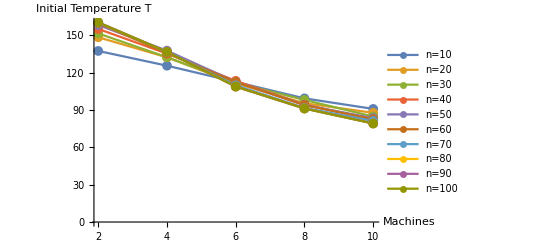

```mathematica
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotinitialTemp[2,100,currentDir,nList,mList]
```

```mathematica
T=100;
f1[x_]:=T 0.08^x;
f2[x_]:=T-x;
f3[x_]:=1/(1+x)T;
f4[x_]:=1/(1+x^2)T;
```

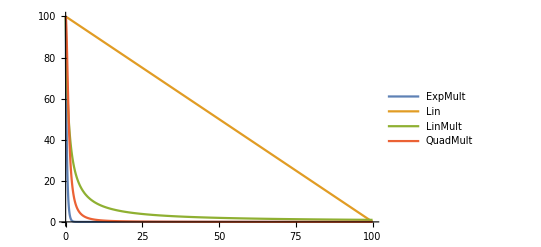

```mathematica
Plot[{f1[x],f2[x],f3[x],f4[x]},{x,0,100},PlotLegends->{"ExpMult","Lin","LinMult","QuadMult"}]
```